```mathematica
{LabelStyle->18,PlotLabel->"Plot Label",AxesLabel->{"X","Y"}}
raspberryPi=FileNameJoin[{"Z:","RbData","2017-10-28"}];
laptop=FileNameJoin[{"/","home","karl"}];
labComp=FileNameJoin[{"C:","Users","kahrendsen2"}];
dropboxOn=FileNameJoin[{"Dropbox","00School","research","DataRuns"}];
folder=FileNameJoin[{laptop,dropboxOn}];
SetDirectory[folder];
files=FileNames["*"]
SetOptions[Plot,BaseStyle->{FontSize->24},ImageSize->Large];

plotLabel="Plot Label";
yAxisLabel="Y";
xAxisLabel="X";
ps={LabelStyle->18,PlotLabel->plotLabel,AxesLabel->{xAxisLabel,yAxisLabel}}
```

{LabelStyle→18,PlotLabel→Plot Label,AxesLabel→{X,Y}}

{15-06-09_USBCounterError,15-07-06mockPolarizationData,16-01-14,16-01-21_Data,16-05-25_PolarizationData,16-07-06_PolarizationData,16-08-04_PolarizationData,16-08-07_HeliumTargetPictures,16-08-09_PolarizationData,16-10-17_polarimeter,16-10-27_DataReport,16-11-03_faradayRotation,16-11-07_faradayRotation,16-11-18_faradayRotation,16-12-09_faradayRotation,17-01-31,17-02-17_plusMinus,17-03-06_PlusMinusWavemeter,17-03-10_non-RbFaradayRotation,17-03-15_AimingFor5e12,17-03-15_wavemeterNoRb,17-03-28,17-03-29_pumpLaserFindingCircular,17-03-30_WavemeterReliability,17-04-04_polarization,17-04-06_polarization,17-04-07_wmReliability,17-04-18,17-04-18_polarization,17-04-22,17-04-25_ProbePolarizationDriftOpenChamber,17-04-30_laserReport,17-05-17_DirtyGunRun,17-05-18_ProbeDrift,17-05-19_BetterLaser,17-05-24_SimplifiedPolarization,17-05-25_LaserProfiling,17-06-02,17-06-06_IntensityOfProbeStudy,17-06-11,17-06-13,17-06-16,17-06-17,17-06-25,17-07-01_nRbVsBufferGasAnalysis,17-07-01_PumpLaserAnalysis,17-07-03_lowerNRb_BGPStudy,17-07-03_ProbeDrift,17-07-03_pumpBroadening,17-07-06_lotsOfProbeMeasurements,17-07-06_MagneticField,17-07-06_probePower,17-07-12_polVsPumpPower,17-08-01_rgaInitialScans,17-08-03_redoingSystemDiagnostic,17-08-06_probeDrift,17-08-18_furtherPolarizationStudy,17-08-19_furtherPolarizationStudy2,17-08-22_furtherPolarizationStudyFoundLeak,17-08-29_BvsProbePower_probeDetuneVsMagnetRot,17-09-05_Polarizations_100mTBGP,17-09-20,17-10-03_ElectronGun,17-10-16_ElectronGun,17-10-24_UnpolarizedPolarization,17-10-26_24And30eVRuns,17-10-28_24and30eVRedux,17-11-04_MoreUnpolarizedRuns,17-11-06_UnpolarizedRuns2,17-11-15_BalancedPhotoDetector,17-11-18_SystemDiagnosis,17-12-18_SystemDiagnosis,17-12-20_PolarizingElectrons,18-01-03_PolarizingElectrons,18-01-04_PolarizingElectrons,18-01-10_ChamberWarming,18-01-11_SystemDiagnostics,18-01-12_recreatingPolFigure,18-01-13_recreatingPolFigureIncreasedT,18-01-16_morePolarization,18-01-20_electronPolarization,dataDump,wavemeterOffsets}

{LabelStyle→18,PlotLabel→Plot Label,AxesLabel→{X,Y}}

```mathematica
SetDirectory[FileNameJoin[{folder,"18-01-20_electronPolarization","data"}]];
files=FileNames["EX*.dat"]
```

{EX2018-01-20_194206.dat,EX2018-01-20_221123.dat,EX2018-01-21_005105.dat,EX2018-01-21_010728.dat,EX2018-01-21_015806.dat,EX2018-01-21_022915.dat,EX2018-01-21_030023.dat,EX2018-01-21_033131.dat,EX2018-01-21_040238.dat,EX2018-01-21_043345.dat,EX2018-01-21_114835.dat}

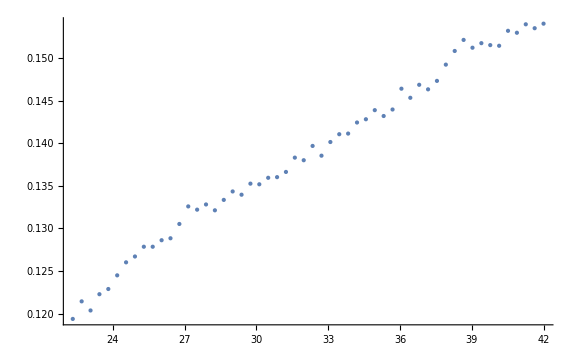

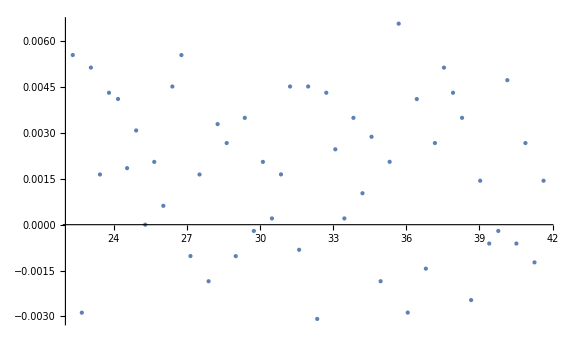

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NumberForm::sigz: In addition to the number of digits requested, one or more zeros will appear as placeholders.

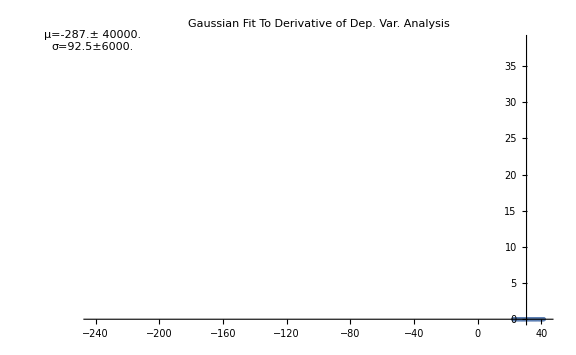

ListPlot::lpn: data2 is not a list of numbers or pairs of numbers.

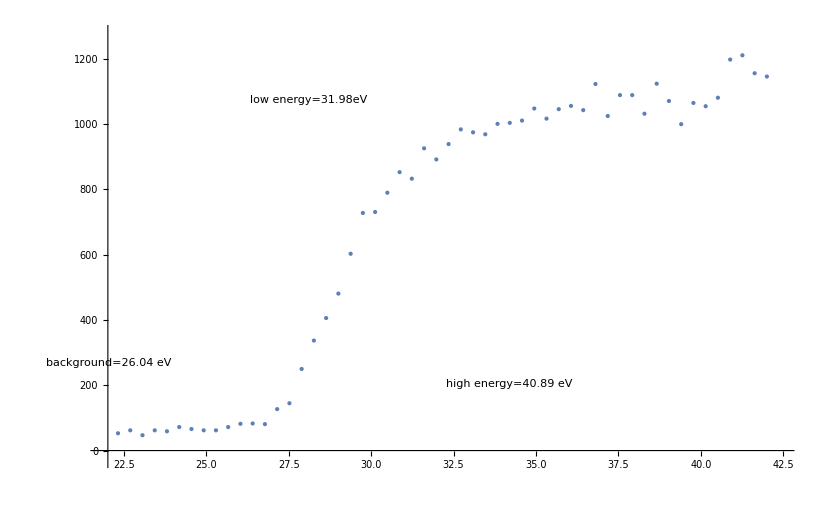

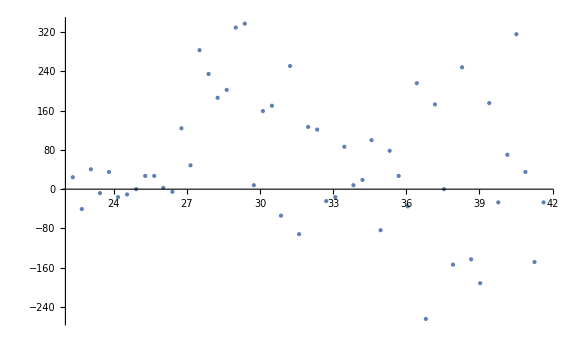

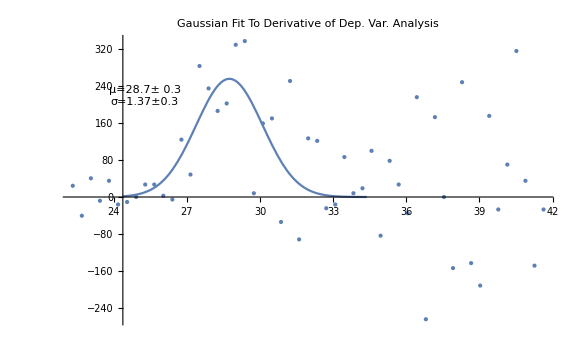

ListPlot::lpn: data2 is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot::lpn: data2 is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

```mathematica
ExcitationFunctionProcessor["221123"]
```

```mathematica
GetFileHeaderInfo[dataFileName_]:=Module[{rawFile,data,association,k},
rawFile=Import[dataFileName];
data={};
association=Association[];
k=1;
While[StringPart[rawFile[[k]][[1]],1]=="#",
association=Append[association,rawFile[[k]][[1]]->rawFile[[k]][[2]]];
k++;
];
association
];
GetFileDataset[dataFileName_]:=Module[{rawFile,headerStrippedData,columnHeaderLineNumber,lastColumnToImport,j,k,ass,tabularData,ds,rbAbsorptionRef,rbAbsorptionPro},
rawFile=Import[dataFileName];
k=1;

While[StringPart[rawFile[[k]][[1]],1]=="#",
k++;
];


headerStrippedData=Take[rawFile,{k,-1},All];
tabularData={};
For[j=2,j≤Length[headerStrippedData],j++,
If[Length[headerStrippedData[[j]]]>1,
ass=Association[];
For[k=1,k≤Length[headerStrippedData[[j]]],k++,
ass=Append[ass,headerStrippedData[[1]][[k]]->headerStrippedData[[j]][[k]]];
];
tabularData=Append[tabularData,ass];
]
];
ds =Dataset[tabularData]
];

GaussianAnalyzer[timeString_,dependentVariableString_]:=Module[{file,ps,header,data,energy,energyDiff,depVar,depVarDiff,energyOneRemoved,depVarDer,plotTitle,plotData,plotData2,fit,model,pe,errors,gaussModel,m,σ,x,ampl,maxDerPos,energyOfPeak,dataLabel1,dataLabel2,x1,y1},
file=FileNames["*"<>ToString[timeString]<>".dat"][[1]];

header=GetFileHeaderInfo[file];
data=GetFileDataset[file];
energy=Reverse[Normal[data[All,"SecondaryElectronEnergy"]]];
depVar=Reverse[Normal[data[All,dependentVariableString]]];
depVarDiff=Differences[depVar];
energyDiff=Differences[energy];
energyOneRemoved=Take[energy,{1,-2}];
depVarDer=depVarDiff/energyDiff;
Print[ListPlot[Transpose[{energy,depVar}]]];
Print[ListPlot[Transpose[{energyOneRemoved,depVarDer}]]];


plotTitle="Gaussian Analysis";

plotData=Transpose[{energy,depVar}];
plotData2=Transpose[{energyOneRemoved,depVarDer}];


(*
yAxisTitle="d(Counts)/d(Energy)";
xAxisTitle="Electron Energy (eV)";
*)
dataLabel1="Data";
dataLabel2="Derivative";

ps={ImageSize->Large, PlotLabel->plotTitle,AxesLabel->{"X","Y"}};

plotData=plotData2;
gaussModel[x_]=ampl Evaluate[PDF[NormalDistribution[m,σ],x]];
(*Find the position of the peak of the derivative data*)
maxDerPos=Position[depVarDer,Max[depVarDer]][[1]];
energyOfPeak=energyOneRemoved[[maxDerPos]][[1]];

fit=NonlinearModelFit[plotData,gaussModel[x],{ampl,{m,energyOfPeak},σ},x];
model=Normal[fit];
pe=fit["BestFitParameters"]; (*Parameter Estimates*)
errors=fit["ParameterErrors"];


x1=energyOfPeak-(3σ/.pe);
y1=.25*(ampl)/.pe;
fitInfo=StringForm["μ=``± ``\nσ=``±``",NumberForm[m/.pe,3],NumberForm[errors[[2]],1],NumberForm[σ/.pe,3],NumberForm[errors[[3]],1]];
Print[Show[{Plot[gaussModel[x]/.pe,{x,energyOfPeak-5,energyOfPeak+5},PlotRange->All,PlotLabel->"Gaussian Fit To Derivative\nof Dep. Var. Analysis"],
Graphics[Text[fitInfo,{x1,y1}],BaseStyle->15],
ListPlot[plotData,PlotLabel->"PLOT2"]}]];
bothPlot=ListPlot[{Legended[plotData,dataLabel2],Legended[plotData2,dataLabel1]}];
derivativePlot=ListPlot[Legended[data2,dataLabel2],ps];

entry ={header["#Filename:"],header["#CVGauge(N2)(Torr):"],data[1,"N2Offset"],data[1,"bias"],m/.pe, σ/.pe,depVar[[1]],depVar[[-1]]}
];

ExcitationFunctionProcessor[timeString_]:=Module[{file,ps,header,data,energy,energyDiff,current,currentDiff,energyOneRemoved,currentDer,plotTitle,plotData,plotData2,fit,model,pe,errors,gaussModel,m,σ,x,ampl,maxDerPos,energyOfPeak,x1,y1},
GaussianAnalyzer[timeString,"Current"];
GaussianAnalyzer[timeString,"Count"];
];
```

```mathematica
file=FileNames["*"<>ToString[221123]<>".dat"][[1]];

header=GetFileHeaderInfo[file];
data=GetFileDataset[file]
belowThreshold=Normal[data[Select[#PrimaryElectronEnergy < 24.4-3*.7&],"Count"]]
averageBelowThreshold=N[Mean[belowThreshold]]
stdDevBelowThreshold=N[MeanDeviation[belowThreshold]]
```

Dataset[<>]

{}

Mean[{}]

MeanDeviation::vecmat1: Argument {} is neither a non-empty vector nor a non-empty matrix.

MeanDeviation[{}]